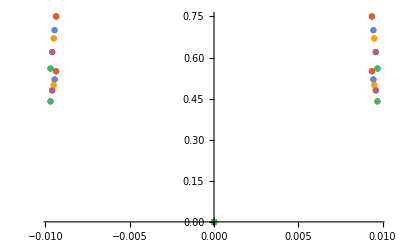

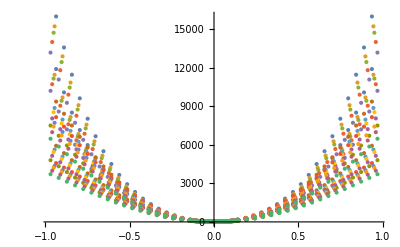

```mathematica
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,15}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,15}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,15}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,15}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
```

```mathematica
Clear[α,β,γ]
(*define 4th order potentials along 001 (alpha) 011 (beta) and 111 (gamma)*)
V[1,2,α][[1]]
V[1,2,β][[6]]
V[1,2,γ][[11]]
rule1={α->(x/Sqrt[1]),α->(y/Sqrt[1]),α->(z/Sqrt[1])}
rule2={β->((x+y)),β->((x-y)),β->((y+z)),β->((y-z)),β->((z+x)),β->((z-x))}
rule3={γ->((x+y+z)),γ->((x+y-z)),γ->((x-y+z)),γ->((x-y-z))}
```

6264.46 α^2

6264.46 β^2

6264.46 γ^2

{α→x,α→y,α→z}

{β→x+y,β→x-y,β→y+z,β→y-z,β→x+z,β→-x+z}

{γ→x+y+z,γ→x+y-z,γ→x-y+z,γ→x-y-z}

```mathematica
U1[e_,o_,x_,y_,z_]:=(3/3)*Sum[V[e,o,α][[1]]/.rule1[[i]],{i,1,3}]//Simplify
U2[e_,o_,x_,y_,z_]:=(3/12)*Sum[V[e,o,β][[6]]/.rule2[[i]],{i,1,6}]//Simplify
U3[e_,o_,x_,y_,z_]:=(3/12)*Sum[V[e,o,γ][[11]]/.rule3[[i]],{i,1,4}]//Simplify
UUU[e_,o_,x_,y_,z_]:=U1[e,o,x,y,z]+(U2[e,o,x,y,z]-U1[e,o,x,y,z])+(U3[e,o,x,y,z]-(U1[e,o,x,y,z]+(U2[e,o,x,y,z]-U1[e,o,x,y,z])))
(*CHECK 4TH ORDERS*)
V[1,4,x][[1]]
U1[1,4,x,y,z]/.{z->0,y->0}//Simplify
V[1,4,x][[6]]
U2[1,4,x,y,z]/.{z->0,y->0}//Simplify
V[1,4,x][[11]]
U3[1,4,x,y,z]/.{z->0,y->0}//Simplify
(*CHECK 6TH ORDERS*)
V[1,6,x][[1]]
U1[1,6,x,y,z]/.{z->0,y->0}//Simplify
V[1,6,x][[6]]
U2[1,6,x,y,z]/.{z->0,y->0}//Simplify
V[1,6,x][[11]]
U3[2,6,x,y,z]/.{z->0,y->0}//Simplify
UUU[2,6,x,y,z]/.{z->0,y->0}//Simplify
(*All good*)
```

5774.79 x^2+8775.82 x^4

0.+5774.79 x^2+8775.82 x^4

6483.37 x^2+345.503 x^4

0.+6483.37 x^2+345.503 x^4

6383.51 x^2-1319.62 x^4

0.+6383.51 x^2-1319.62 x^4

6256.47 x^2+6879.88 x^4+1626.02 x^6

0.+6256.47 x^2+6879.88 x^4+1626.02 x^6

6237.52 x^2+1313.17 x^4-829.898 x^6

0.+6237.52 x^2+1313.17 x^4-829.898 x^6

6282.42 x^2-921.722 x^4-341.247 x^6

0.+8674.74 x^2+2437.17 x^4-1984.51 x^6

0.+8674.74 x^2+2437.17 x^4-1984.51 x^6

```mathematica
U1[1,6,x,y,z]
U2[1,6,x,y,z]//Simplify
U3[2,6,x,y,z]//Expand
UUU[2,4,x,y,z]
```

6256.47 x^2+6879.88 x^4+1626.02 x^6+6256.47 y^2+6879.88 y^4+1626.02 y^6+6256.47 z^2+6879.88 z^4+1626.02 z^6

0.-829.898 x^6-829.898 y^6+6237.52 z^2+1313.17 z^4-829.898 z^6+y^4 (1313.17-6224.24 z^2)+x^4 (1313.17-6224.24 y^2-6224.24 z^2)+y^2 (6237.52+3939.5 z^2-6224.24 z^4)+x^2 (6237.52+3939.5 y^2-6224.24 y^4+3939.5 z^2-6224.24 z^4)

0.+8674.74 x^2+2437.17 x^4-1984.51 x^6+8674.74 y^2+14623. x^2 y^2-29767.6 x^4 y^2+2437.17 y^4-29767.6 x^2 y^4-1984.51 y^6+8674.74 z^2+14623. x^2 z^2-29767.6 x^4 z^2+14623. y^2 z^2-178606. x^2 y^2 z^2-29767.6 y^4 z^2+2437.17 z^4-29767.6 x^2 z^4-29767.6 y^2 z^4-1984.51 z^6

0.+123.228 x^4+123.228 y^4+9262.62 z^2+123.228 z^4+y^2 (9262.62+739.37 z^2)+x^2 (9262.62+739.37 y^2+739.37 z^2)

```mathematica
U1[1,6,x,y,z]/.{x->0,y->0}
V[1,6,z][[11]]
U2[1,4,x,y,z]/.{y->0,z->0}
U3[1,4,x,y,z]/.{y->0,z->0}
```

0.+6256.47 z^2+6879.88 z^4+1626.02 z^6

6282.42 z^2-921.722 z^4-341.247 z^6

0.+6483.37 x^2+345.503 x^4

0.+6383.51 x^2-1319.62 x^4

```mathematica
(*C harmonic*)
UUU[2,4,x,y,z]//Expand
(*Zr 12th order anharmonic*)
UUU[2,4,x,y,z]/.{y->0,z->0}//Expand
```

0.+9262.62 x^2+123.228 x^4+9262.62 y^2+739.37 x^2 y^2+123.228 y^4+9262.62 z^2+739.37 x^2 z^2+739.37 y^2 z^2+123.228 z^4

0.+9262.62 x^2+123.228 x^4

```mathematica
contourOptions={AxesLabel->{"x (Å)","z (Å)"},ImageSize->300};
```

```mathematica
cHar=Table[With[{B=0.25*i},ContourPlot[UUU[1,2,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,1}];
cAnh=Table[With[{B=0.25*i},ContourPlot[UUU[1,6,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,1}];
zHar=Table[With[{B=0.25*i},ContourPlot[UUU[2,2,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,1}];
zAnh=Table[With[{B=0.25*i},ContourPlot[UUU[2,6,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,1}];
```

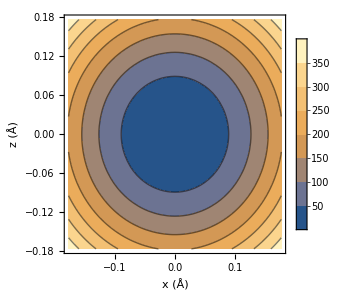
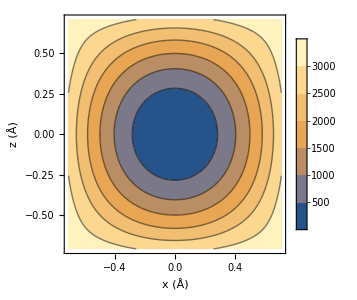

```mathematica
(*Carbon  anharmonic  - small and large scale*)
Table[With[{B=0.25*i},ContourPlot[UUU[1,6,x,y,z]/.y->0,{x,-B/Sqrt[2],B/Sqrt[2]},{z,-B/Sqrt[2],B/Sqrt[2]},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4,3}]
```

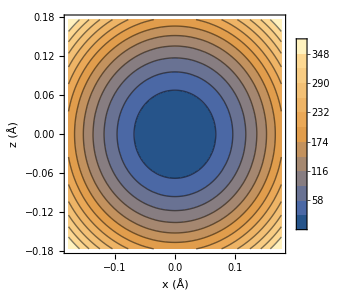
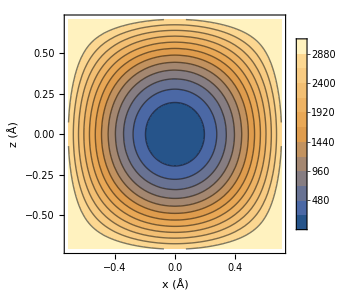

```mathematica
(*Carbon  anharmonic  - small and large scale - more contours*)
Table[With[{B=0.25*i},ContourPlot[UUU[1,6,x,y,z]/.y->0,{x,-B/Sqrt[2],B/Sqrt[2]},{z,-B/Sqrt[2],B/Sqrt[2]},PlotLegends->Automatic,Contours->12,Evaluate@contourOptions]],{i,1,4,3}]
```

```mathematica
(*Carbon and Zirconium, harmonic and anharmonic - larger scale*)
GraphicsGrid[{{cHar[[2]],cAnh[[2]]},{zHar[[2]],zAnh[[2]]}},ImageSize->1000]
```

-Graphics-

```mathematica
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46,5810.6,5528.52,5208.33,4676.37}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978,31.1058,30.3414,29.4497,27.9052}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8542.44,7821.96,7408.22,6727.43,5951.75}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.6852,13.0954,12.7443,12.1447,11.4231}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=84;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒharc=-(1/(2m[[1]]))*Laplacian[u[x,y,z],{x,y,z}]+UUU[1,2,x,y,z]*u[x,y,z]
ℒanhc=-(1/(2m[[1]]))*Laplacian[u[x,y,z],{x,y,z}]+UUU[1,6,x,y,z]*u[x,y,z]
ℒharz=-(1/(2m[[2]]))*Laplacian[u[x,y,z],{x,y,z}]+UUU[1,2,x,y,z]*u[x,y,z]
ℒanhz=-(1/(2m[[2]]))*Laplacian[u[x,y,z],{x,y,z}]+UUU[1,6,x,y,z]*u[x,y,z]
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->10000}}};
```

(0.+6264.46 x^2+6264.46 y^2+6264.46 z^2) u[x,y,z]-0.0416295 (u^(0,0,2)[x,y,z]+u^(0,2,0)[x,y,z]+u^(2,0,0)[x,y,z])

(0.+1/4 (0.-1364.99 x^6-1364.99 y^6+25129.7 z^2-3686.89 z^4-1364.99 z^6+y^4 (-3686.89-20474.8 z^2)+x^4 (-3686.89-20474.8 y^2-20474.8 z^2)+y^2 (25129.7-22121.3 z^2-20474.8 z^4)+x^2 (25129.7-20474.8 y^4-22121.3 z^2-20474.8 z^4+y^2 (-22121.3-122849. z^2)))) u[x,y,z]-0.0416295 (u^(0,0,2)[x,y,z]+u^(0,2,0)[x,y,z]+u^(2,0,0)[x,y,z])

(0.+6264.46 x^2+6264.46 y^2+6264.46 z^2) u[x,y,z]-0.00548101 (u^(0,0,2)[x,y,z]+u^(0,2,0)[x,y,z]+u^(2,0,0)[x,y,z])

(0.+1/4 (0.-1364.99 x^6-1364.99 y^6+25129.7 z^2-3686.89 z^4-1364.99 z^6+y^4 (-3686.89-20474.8 z^2)+x^4 (-3686.89-20474.8 y^2-20474.8 z^2)+y^2 (25129.7-22121.3 z^2-20474.8 z^4)+x^2 (25129.7-20474.8 y^4-22121.3 z^2-20474.8 z^4+y^2 (-22121.3-122849. z^2)))) u[x,y,z]-0.00548101 (u^(0,0,2)[x,y,z]+u^(0,2,0)[x,y,z]+u^(2,0,0)[x,y,z])

```mathematica
harc=NDEigensystem[ℒharc,u[x,y,z],{x,-B/2,B/2},{y,-B/2,B/2},{z,-B/2,B/2},Neigenvalues,Evaluate@solverOptions]//Timing;
harz=NDEigensystem[ℒharz,u[x,y,z],{x,-B/2,B/2},{y,-B/2,B/2},{z,-B/2,B/2},Neigenvalues,Evaluate@solverOptions]//Timing;
```

```mathematica
"Timing:"
harc[[1]]
harz[[1]]
```

Timing:

78.4709

47.4857

```mathematica
hanhc=NDEigensystem[ℒanhc,u[x,y,z],{x,-B/2,B/2},{y,-B/2,B/2},{z,-B/2,B/2},Neigenvalues,Evaluate@solverOptions]//Timing;
hanhz=NDEigensystem[ℒanhz,u[x,y,z],{x,-B/2,B/2},{y,-B/2,B/2},{z,-B/2,B/2},Neigenvalues,Evaluate@solverOptions]//Timing;
```

```mathematica
"Timing:"
hanh[[1]]
hanh[[1]]
```

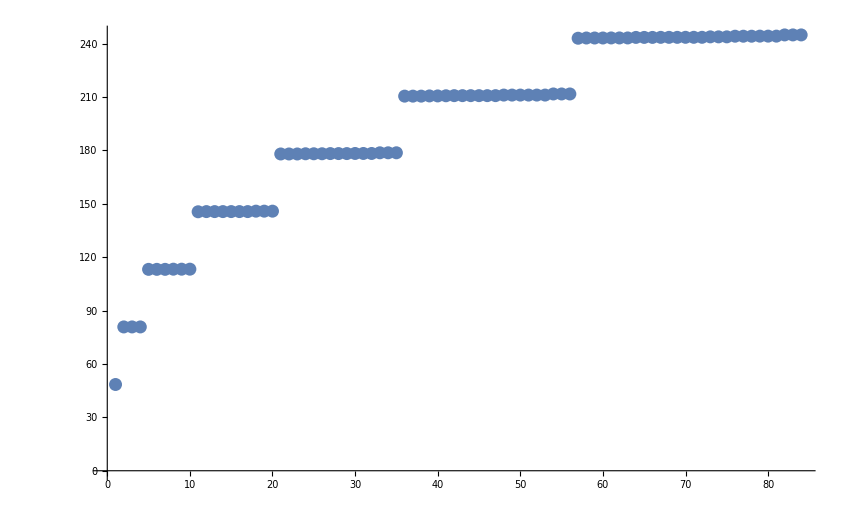

```mathematica
ListPlot@harc[[2]][[1]]
```

```mathematica
(*ED QHO - occupation numbers go (i + 3/2) instead of (i +1/2): 1.5,2.5,3.5...*)
(*i degeneracy d is given by d=(i+1)(i+2)/2 : 1,  *)
```

```mathematica
(*Degeneracies*)
Table[(i+1)*(i+2)/2,{i,0,6}]
(*Excitation numbers*)
(*So equal to 3 indepdent 1DQHO*)
Table[i+3/2,{i,0,6}]/3//N
```

{1,3,6,10,15,21,28}

{0.5,0.833333,1.16667,1.5,1.83333,2.16667,2.5}

```mathematica
(harc[[2]][[1]])/(2harc[[2]][[1]][[1]])
```

{0.5,0.83371,0.83371,0.83371,1.16748,1.16748,1.16748,1.16843,1.16843,1.16853,1.50132,1.50235,1.50235,1.50235,1.5024,1.5024,1.5024,1.50483,1.50483,1.50483,1.83635,1.83635,1.83635,1.83753,1.83753,1.8376,1.83866,1.83866,1.83866,1.83928,1.83928,1.83928,1.84319,1.84319,1.84326,2.17167,2.17167,2.17167,2.17287,2.17287,2.17378,2.17448,2.17448,2.17448,2.17452,2.17452,2.17452,2.17779,2.17779,2.17779,2.17783,2.17783,2.17783,2.18422,2.18422,2.18422,2.50727,2.50867,2.50867,2.50867,2.509,2.509,2.509,2.51211,2.51211,2.51211,2.51245,2.51245,2.51245,2.51265,2.51269,2.51269,2.5153,2.5153,2.51533,2.51902,2.51902,2.51902,2.51953,2.51953,2.51953,2.52651,2.52651,2.52654}

```mathematica
GraphicsGrid[Table[Table[ContourPlot[harc[[2]][[2]][[i]]/.x->0,{y,-B/4,B/4},{z,-B/4,B/4}],{i,5j-4,5j}],{j,1,10}],ImageSize->1200]
```

```mathematica
GraphicsGrid[{Table[ContourPlot[test[[2]][[2]][[i]]/.x->0,{y,-B/5,B/5},{z,-B/5,B/5}],{i,1,5}],Table[ContourPlot[test[[2]][[2]][[i]]/.x->0,{y,-B/5,B/5},{z,-B/5,B/5}],{i,6,10}],Table[ContourPlot[test[[2]][[2]][[i]]/.x->0,{y,-B/5,B/5},{z,-B/5,B/5}],{i,11,15}],Table[ContourPlot[test[[2]][[2]][[i]]/.x->0,{y,-B/5,B/5},{z,-B/5,B/5}],{i,16,20}],Table[ContourPlot[test[[2]][[2]][[i]]/.x->0,{y,-B/5,B/5},{z,-B/5,B/5}],{i,21,25}]},ImageSize->1200]
```

-Graphics-

```mathematica
ContourPlot3D[test[[2]][[2]][[1]]/.{x->x,y->y,z->z},{x,-B/5,B/5},{y,-B/5,B/5},{z,-B/5,B/5}]
```

-Graphics3D-

```mathematica
eigensysCanh=NDEigensystem[ℒanhc,u[x,y,z],{{x,-B,B},{y,-B,B},{z,-B,B}},Neigenvalues,Evaluate@solverOptions]
```

```mathematica
Clear[R,θ,ϕ]
```

```mathematica
UUU[x,y,z]
```

UUU[x,y,z]

```mathematica
Transformation to polar field
SUUU[e_,o_,R,θ,ϕ]:=TransformedField["Cartesian"->"Spherical",UUU[e,o,x,y,z],{x,y,z}->{R,θ,ϕ}]
```

field polar to Transformation

```mathematica
SUUU[1,12,R,θ,ϕ]
SUUU[1,2,R,θ,ϕ]
SUUU[2,2,R,θ,ϕ]
```

-37.3075 (0.-167.878 R^2 Cos[θ]^2+21.087 R^4 Cos[θ]^4+15.6751 R^6 Cos[θ]^6-1.7712 R^8 Cos[θ]^8-2.91718 R^10 Cos[θ]^10+1. R^12 Cos[θ]^12-167.878 R^2 Cos[ϕ]^2 Sin[θ]^2+126.522 R^4 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+235.127 R^6 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-49.5936 R^8 Cos[θ]^6 Cos[ϕ]^2 Sin[θ]^2-131.273 R^10 Cos[θ]^8 Cos[ϕ]^2 Sin[θ]^2+66. R^12 Cos[θ]^10 Cos[ϕ]^2 Sin[θ]^2+21.087 R^4 Cos[ϕ]^4 Sin[θ]^4+235.127 R^6 Cos[θ]^2 Cos[ϕ]^4 Sin[θ]^4-123.984 R^8 Cos[θ]^4 Cos[ϕ]^4 Sin[θ]^4-612.609 R^10 Cos[θ]^6 Cos[ϕ]^4 Sin[θ]^4+495. R^12 Cos[θ]^8 Cos[ϕ]^4 Sin[θ]^4+15.6751 R^6 Cos[ϕ]^6 Sin[θ]^6-49.5936 R^8 Cos[θ]^2 Cos[ϕ]^6 Sin[θ]^6-612.609 R^10 Cos[θ]^4 Cos[ϕ]^6 Sin[θ]^6+924. R^12 Cos[θ]^6 Cos[ϕ]^6 Sin[θ]^6-1.7712 R^8 Cos[ϕ]^8 Sin[θ]^8-131.273 R^10 Cos[θ]^2 Cos[ϕ]^8 Sin[θ]^8+495. R^12 Cos[θ]^4 Cos[ϕ]^8 Sin[θ]^8-2.91718 R^10 Cos[ϕ]^10 Sin[θ]^10+66. R^12 Cos[θ]^2 Cos[ϕ]^10 Sin[θ]^10+1. R^12 Cos[ϕ]^12 Sin[θ]^12-167.878 R^2 Sin[θ]^2 Sin[ϕ]^2+126.522 R^4 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+235.127 R^6 Cos[θ]^4 Sin[θ]^2 Sin[ϕ]^2-49.5936 R^8 Cos[θ]^6 Sin[θ]^2 Sin[ϕ]^2-131.273 R^10 Cos[θ]^8 Sin[θ]^2 Sin[ϕ]^2+66. R^12 Cos[θ]^10 Sin[θ]^2 Sin[ϕ]^2+126.522 R^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+1410.76 R^6 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2-743.904 R^8 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2-3675.65 R^10 Cos[θ]^6 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+2970. R^12 Cos[θ]^8 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+235.127 R^6 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2-743.904 R^8 Cos[θ]^2 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2-9189.13 R^10 Cos[θ]^4 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2+13860. R^12 Cos[θ]^6 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2-49.5936 R^8 Cos[ϕ]^6 Sin[θ]^8 Sin[ϕ]^2-3675.65 R^10 Cos[θ]^2 Cos[ϕ]^6 Sin[θ]^8 Sin[ϕ]^2+13860. R^12 Cos[θ]^4 Cos[ϕ]^6 Sin[θ]^8 Sin[ϕ]^2-131.273 R^10 Cos[ϕ]^8 Sin[θ]^10 Sin[ϕ]^2+2970. R^12 Cos[θ]^2 Cos[ϕ]^8 Sin[θ]^10 Sin[ϕ]^2+66. R^12 Cos[ϕ]^10 Sin[θ]^12 Sin[ϕ]^2+21.087 R^4 Sin[θ]^4 Sin[ϕ]^4+235.127 R^6 Cos[θ]^2 Sin[θ]^4 Sin[ϕ]^4-123.984 R^8 Cos[θ]^4 Sin[θ]^4 Sin[ϕ]^4-612.609 R^10 Cos[θ]^6 Sin[θ]^4 Sin[ϕ]^4+495. R^12 Cos[θ]^8 Sin[θ]^4 Sin[ϕ]^4+235.127 R^6 Cos[ϕ]^2 Sin[θ]^6 Sin[ϕ]^4-743.904 R^8 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^6 Sin[ϕ]^4-9189.13 R^10 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^6 Sin[ϕ]^4+13860. R^12 Cos[θ]^6 Cos[ϕ]^2 Sin[θ]^6 Sin[ϕ]^4-123.984 R^8 Cos[ϕ]^4 Sin[θ]^8 Sin[ϕ]^4-9189.13 R^10 Cos[θ]^2 Cos[ϕ]^4 Sin[θ]^8 Sin[ϕ]^4+34650. R^12 Cos[θ]^4 Cos[ϕ]^4 Sin[θ]^8 Sin[ϕ]^4-612.609 R^10 Cos[ϕ]^6 Sin[θ]^10 Sin[ϕ]^4+13860. R^12 Cos[θ]^2 Cos[ϕ]^6 Sin[θ]^10 Sin[ϕ]^4+495. R^12 Cos[ϕ]^8 Sin[θ]^12 Sin[ϕ]^4+15.6751 R^6 Sin[θ]^6 Sin[ϕ]^6-49.5936 R^8 Cos[θ]^2 Sin[θ]^6 Sin[ϕ]^6-612.609 R^10 Cos[θ]^4 Sin[θ]^6 Sin[ϕ]^6+924. R^12 Cos[θ]^6 Sin[θ]^6 Sin[ϕ]^6-49.5936 R^8 Cos[ϕ]^2 Sin[θ]^8 Sin[ϕ]^6-3675.65 R^10 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^8 Sin[ϕ]^6+13860. R^12 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^8 Sin[ϕ]^6-612.609 R^10 Cos[ϕ]^4 Sin[θ]^10 Sin[ϕ]^6+13860. R^12 Cos[θ]^2 Cos[ϕ]^4 Sin[θ]^10 Sin[ϕ]^6+924. R^12 Cos[ϕ]^6 Sin[θ]^12 Sin[ϕ]^6-1.7712 R^8 Sin[θ]^8 Sin[ϕ]^8-131.273 R^10 Cos[θ]^2 Sin[θ]^8 Sin[ϕ]^8+495. R^12 Cos[θ]^4 Sin[θ]^8 Sin[ϕ]^8-131.273 R^10 Cos[ϕ]^2 Sin[θ]^10 Sin[ϕ]^8+2970. R^12 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^10 Sin[ϕ]^8+495. R^12 Cos[ϕ]^4 Sin[θ]^12 Sin[ϕ]^8-2.91718 R^10 Sin[θ]^10 Sin[ϕ]^10+66. R^12 Cos[θ]^2 Sin[θ]^10 Sin[ϕ]^10+66. R^12 Cos[ϕ]^2 Sin[θ]^12 Sin[ϕ]^10+1. R^12 Sin[θ]^12 Sin[ϕ]^12)

6264.46 R^2 Cos[θ]^2+6264.46 R^2 Cos[ϕ]^2 Sin[θ]^2+6264.46 R^2 Sin[θ]^2 Sin[ϕ]^2

8542.44 R^2 Cos[θ]^2+8542.44 R^2 Cos[ϕ]^2 Sin[θ]^2+8542.44 R^2 Sin[θ]^2 Sin[ϕ]^2

```mathematica
(*Harmonic C and Zr*)
GraphicsGrid[{{SphericalPlot3D[Evaluate[SUUU[1,2,R,θ,ϕ]/.R->1],{θ,0,Pi},{ϕ,0,2Pi}],SphericalPlot3D[Evaluate[SUUU[2,2,R,θ,ϕ]/.R->1],{θ,0,Pi},{ϕ,0,2Pi}]}},ImageSize->700]
(*Anharmonic C and Zr*)
GraphicsGrid[{{SphericalPlot3D[Evaluate[SUUU[1,12,R,θ,ϕ]/.R->1],{θ,0,Pi},{ϕ,0,2Pi}],SphericalPlot3D[Evaluate[SUUU[2,12,R,θ,ϕ]/.R->1],{θ,0,Pi},{ϕ,0,2Pi}]}},ImageSize->700]
```

-Graphics-

-Graphics-

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=4;
ℒharcS=-(1/(2m[[1]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[1,2,R,θ,ϕ]*u[R,θ,ϕ]
ℒharzS=-(1/(2m[[2]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[2,2,R,θ,ϕ]*u[R,θ,ϕ]
ℒanhcS=-(1/(2m[[1]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[1,6,R,θ,ϕ]*u[R,θ,ϕ]
ℒanhzS=-(1/(2m[[2]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[2,6,R,θ,ϕ]*u[R,θ,ϕ]
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0008}}},"Eigensystem"->{"Arnoldi",MaxIterations->10000}}};
```

(6264.46 R^2 Cos[θ]^2+6264.46 R^2 Cos[ϕ]^2 Sin[θ]^2+6264.46 R^2 Sin[θ]^2 Sin[ϕ]^2) u[R,θ,ϕ]-0.0416295 (((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ])

(8542.44 R^2 Cos[θ]^2+8542.44 R^2 Cos[ϕ]^2 Sin[θ]^2+8542.44 R^2 Sin[θ]^2 Sin[ϕ]^2) u[R,θ,ϕ]-0.00548101 (((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ])

-341.247 (-18.4102 R^2 Cos[θ]^2+2.70104 R^4 Cos[θ]^4+1. R^6 Cos[θ]^6-18.4102 R^2 Cos[ϕ]^2 Sin[θ]^2+16.2062 R^4 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+15. R^6 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+2.70104 R^4 Cos[ϕ]^4 Sin[θ]^4+15. R^6 Cos[θ]^2 Cos[ϕ]^4 Sin[θ]^4+1. R^6 Cos[ϕ]^6 Sin[θ]^6-18.4102 R^2 Sin[θ]^2 Sin[ϕ]^2+16.2062 R^4 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+15. R^6 Cos[θ]^4 Sin[θ]^2 Sin[ϕ]^2+16.2062 R^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+90. R^6 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+15. R^6 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2+2.70104 R^4 Sin[θ]^4 Sin[ϕ]^4+15. R^6 Cos[θ]^2 Sin[θ]^4 Sin[ϕ]^4+15. R^6 Cos[ϕ]^2 Sin[θ]^6 Sin[ϕ]^4+1. R^6 Sin[θ]^6 Sin[ϕ]^6) u[R,θ,ϕ]-0.0416295 (((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ])

-1984.51 (-4.37123 R^2 Cos[θ]^2-1.2281 R^4 Cos[θ]^4+1. R^6 Cos[θ]^6-4.37123 R^2 Cos[ϕ]^2 Sin[θ]^2-7.3686 R^4 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+15. R^6 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-1.2281 R^4 Cos[ϕ]^4 Sin[θ]^4+15. R^6 Cos[θ]^2 Cos[ϕ]^4 Sin[θ]^4+1. R^6 Cos[ϕ]^6 Sin[θ]^6-4.37123 R^2 Sin[θ]^2 Sin[ϕ]^2-7.3686 R^4 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+15. R^6 Cos[θ]^4 Sin[θ]^2 Sin[ϕ]^2-7.3686 R^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+90. R^6 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+15. R^6 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2-1.2281 R^4 Sin[θ]^4 Sin[ϕ]^4+15. R^6 Cos[θ]^2 Sin[θ]^4 Sin[ϕ]^4+15. R^6 Cos[ϕ]^2 Sin[θ]^6 Sin[ϕ]^4+1. R^6 Sin[θ]^6 Sin[ϕ]^6) u[R,θ,ϕ]-0.00548101 (((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ])

```mathematica
test=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/2},{θ,0,Pi},{ϕ,-Pi,Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
test[[2]][[1]]/(2test[[2]][[1]][[1]])
```

$Aborted

{0.5,0.887023,0.887023,1.22397}

{0.5,0.566247,0.623846,0.760022}

```mathematica
test=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,-Pi,Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
test[[2]][[1]]/(2test[[2]][[1]][[1]])
```

{0.5,0.707426,0.88885,0.888857}

```mathematica
e
```

```mathematica
harcS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
harzS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
```

```mathematica
hanhcS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
hanhzS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
```

```mathematica
Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]
```

((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ]

```mathematica
"harmonic Timing (C then Zr):"
harcS[[1]]
harzS[[1]]
```

harmonic Timing (C then Zr):

543.888

537.545

```mathematica
"anharmonic Timing (C then Zr):"
hanhcS[[1]]
hanhzS[[1]]
```

anharmonic Timing (C then Zr):

534.822

531.81

```mathematica
GraphicsGrid[{With[{i=81},{SphericalPlot3D[Evaluate[harcS[[2]][[2]][[i]]/.R->0.2],{θ,0,Pi},{ϕ,0,2Pi}],SphericalPlot3D[Evaluate[hanhcS[[2]][[2]][[i]]/.R->0.2],{θ,0,Pi},{ϕ,0,2Pi}]}]},ImageSize->800]
```

-Graphics-

```mathematica
harcS[[2]][[1]]
```

{47.5746,65.8805,81.6599,81.66,97.2244,97.2518,109.394,112.924,112.924,112.925,128.722,128.761,128.763,130.986,144.846,144.854,144.856,144.859,149.656,149.657,161.144,161.182,161.188,161.196,167.448,167.479,177.695,177.697,177.713,177.717,177.721,184.4,184.401,184.401,186.245,194.236,194.278,194.279,194.287,194.296,200.046,200.085,200.085,202.934,210.821,210.823,210.826,210.836,210.84,210.841,214.891,214.899,214.901,214.904,217.605,217.606,227.183,227.244,227.245,227.246,227.246,227.251,229.361,229.375,229.389,229.405,233.,233.035,243.501,243.502,243.502,243.502,243.503,243.503,243.507,243.988,243.996,244.052,244.061,244.079,250.444,250.446,250.449,259.036}

```mathematica
harcS[[2]][[1]]/(2harcS[[2]][[1]][[1]])
```

{0.5,0.692392,0.85823,0.858231,1.02181,1.0221,1.14971,1.18681,1.18681,1.18682,1.35285,1.35325,1.35328,1.37663,1.52231,1.52239,1.52241,1.52244,1.57286,1.57286,1.69359,1.69399,1.69405,1.69414,1.75985,1.76017,1.86754,1.86757,1.86773,1.86777,1.86781,1.93801,1.93802,1.93802,1.9574,2.04138,2.04182,2.04183,2.04192,2.04202,2.10245,2.10285,2.10286,2.13279,2.21569,2.21571,2.21575,2.21585,2.21589,2.21589,2.25846,2.25855,2.25857,2.2586,2.28699,2.287,2.38765,2.38829,2.3883,2.38831,2.38831,2.38836,2.41054,2.41069,2.41083,2.411,2.44879,2.44916,2.55914,2.55916,2.55916,2.55916,2.55917,2.55917,2.55921,2.56427,2.56435,2.56494,2.56504,2.56522,2.63211,2.63214,2.63217,2.72242}

```mathematica
harcS[[2]][[1]]
```

{16.2915,16.3019,16.3332,16.3332,16.3436,16.3748,16.3852,16.4268,16.4581,16.4581,16.4685,16.4997,16.4997,16.5517,16.5517,16.5934,16.6246,16.6662,16.6662,16.6766,16.7078,16.7078,16.7182,16.7599,16.8015,16.8327,16.8327,16.8432,16.9264,16.9577,16.9577,16.9681,16.9681,16.9993,16.9993,17.0409,17.0513,17.1242,17.1242,17.1346,17.1762,17.1763,17.2179,17.3012,17.3324,17.3324,17.3324,17.3324,17.3428,17.3741,17.3741,17.4261,17.4677,17.499,17.499,17.5093,17.5511,17.5926,17.5927,17.6238,17.7071,17.7071,17.7176,17.7906,17.7906,17.8008,17.801,17.8322,17.8322,17.8424,17.8842,17.9258,17.9571,17.9571,17.9986,17.9986,18.0508,18.0509,18.0926,18.1653,18.1653,18.1755,18.2172,18.2174}

```mathematica
harcS[[2]][[1]]/(2harcS[[2]][[1]][[1]])
```

{0.5,0.692392,0.85823,0.858231,1.02181,1.0221,1.14971,1.18681,1.18681,1.18682,1.35285,1.35325,1.35328,1.37663,1.52231,1.52239,1.52241,1.52244,1.57286,1.57286,1.69359,1.69399,1.69405,1.69414,1.75985,1.76017,1.86754,1.86757,1.86773,1.86777,1.86781,1.93801,1.93802,1.93802,1.9574,2.04138,2.04182,2.04183,2.04192,2.04202,2.10245,2.10285,2.10286,2.13279,2.21569,2.21571,2.21575,2.21585,2.21589,2.21589,2.25846,2.25855,2.25857,2.2586,2.28699,2.287,2.38765,2.38829,2.3883,2.38831,2.38831,2.38836,2.41054,2.41069,2.41083,2.411,2.44879,2.44916,2.55914,2.55916,2.55916,2.55916,2.55917,2.55917,2.55921,2.56427,2.56435,2.56494,2.56504,2.56522,2.63211,2.63214,2.63217,2.72242}

```mathematica
(harc[[2]][[1]])/(2harc[[2]][[1]][[1]])
```

{0.5,0.83371,0.83371,0.83371,1.16748,1.16748,1.16748,1.16843,1.16843,1.16853,1.50132,1.50235,1.50235,1.50235,1.5024,1.5024,1.5024,1.50483,1.50483,1.50483,1.83635,1.83635,1.83635,1.83753,1.83753,1.8376,1.83866,1.83866,1.83866,1.83928,1.83928,1.83928,1.84319,1.84319,1.84326,2.17167,2.17167,2.17167,2.17287,2.17287,2.17378,2.17448,2.17448,2.17448,2.17452,2.17452,2.17452,2.17779,2.17779,2.17779,2.17783,2.17783,2.17783,2.18422,2.18422,2.18422,2.50727,2.50867,2.50867,2.50867,2.509,2.509,2.509,2.51211,2.51211,2.51211,2.51245,2.51245,2.51245,2.51265,2.51269,2.51269,2.5153,2.5153,2.51533,2.51902,2.51902,2.51902,2.51953,2.51953,2.51953,2.52651,2.52651,2.52654}

```mathematica
(harcS[[2]][[1]])/(2harcS[[2]][[1]][[1]])
```

{0.5,0.50029,0.501161,0.501161,0.501451}